```mathematica
description="G G -> H A, EW, total decay rate, 1-loop";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

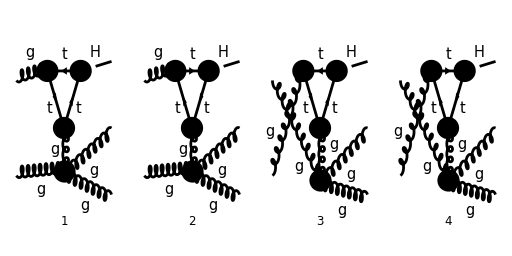

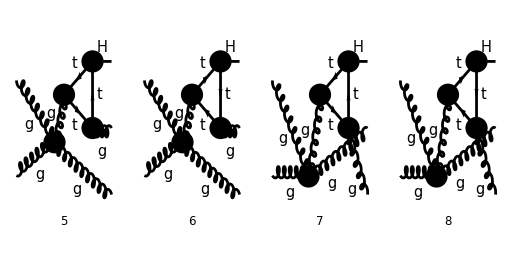

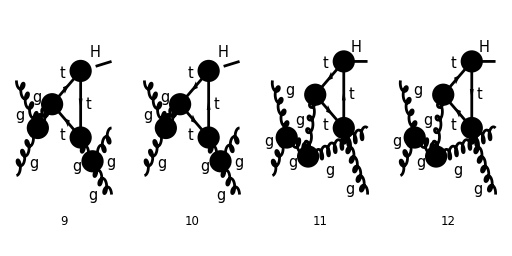

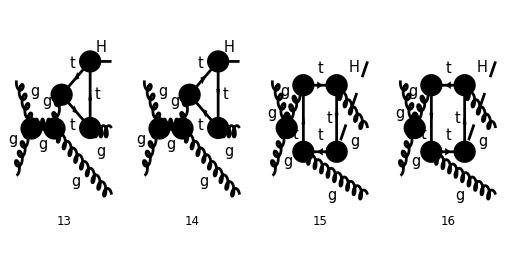

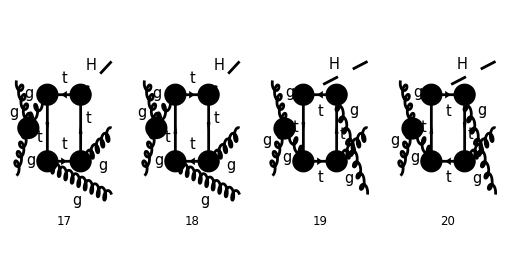

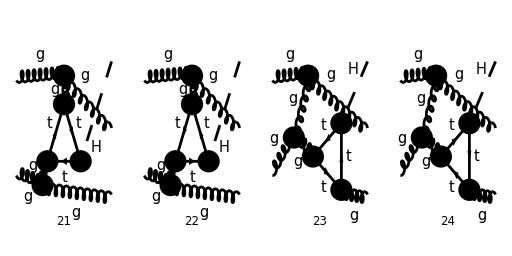

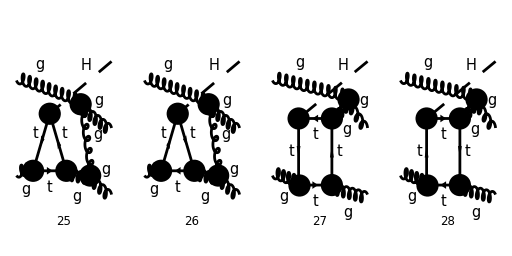

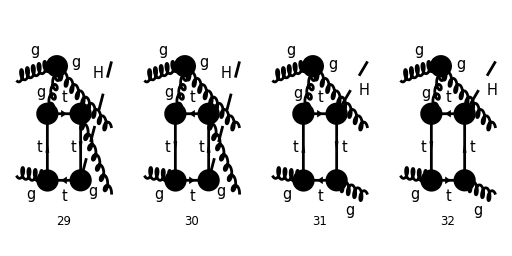

```mathematica
diagsggHgg=InsertFields[CreateTopologies[1,2->3,ExcludeTopologies->{Tadpoles,WFCorrections}],{V[5],V[5]}-> {S[1], V[5], V[5]}, InsertionLevel->{Particles},Model->"SMQCD", ExcludeParticles->{F[4],F[3,{1}],F[3,{2}], V[1],V[2],V[3],V[4]}];

Paint[diagsggHgg,ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
LoopFields[diagsggHqq]
```

LoopFields(TopologyList(Process→{V(5,{Glu1}),V(5,{Glu2})}→{S(1),F(3,{3,Col4}),-F(3,{3,Col5})},Model→{SMQCD},GenericModel→{Lorentz},InsertionLevel→{Particles},ExcludeParticles→{-F(4),F(4),-F(3,{1,_}),F(3,{1,_}),-F(3,{2,_}),F(3,{2,_}),-F(4,{1,_}),F(4,{1,_}),-F(4,{2,_}),F(4,{2,_}),-F(4,{3,_}),F(4,{3,_}),S(2),-S(3),S(3),V(1),V(2),-V(3),V(3)},ExcludeFieldPoints→{},LastSelections→{})(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(6),Field(1)),7,Propagator(FALoop(1))(Vertex(3)(9),Vertex(4)(6),Field(9)))→Insertions(Generic)(11→1),94,1))
 |  |  |  |

```mathematica
LoopFields[DiagramSelect[diagsggHqq, FreeQ[LoopFields[##], V[5]]&]]
```

LoopFields(TopologyList(Process→{V(5,{Glu1}),V(5,{Glu2})}→{S(1),F(3,{3,Col4}),-F(3,{3,Col5})},Model→{SMQCD},GenericModel→{Lorentz},InsertionLevel→{Particles},ExcludeParticles→{-F(4),F(4),-F(3,{1,_}),F(3,{1,_}),-F(3,{2,_}),F(3,{2,_}),-F(4,{1,_}),F(4,{1,_}),-F(4,{2,_}),F(4,{2,_}),-F(4,{3,_}),F(4,{3,_}),S(2),-S(3),S(3),V(1),V(2),-V(3),V(3)},ExcludeFieldPoints→{},LastSelections→{})(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(6),Field(1)),7,Propagator(FALoop(1))(Vertex(3)(9),Vertex(4)(6),Field(9)))→Insertions(Generic)(11→1),94,1))
 |  |  |  |

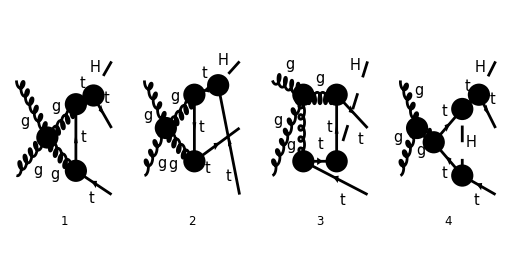

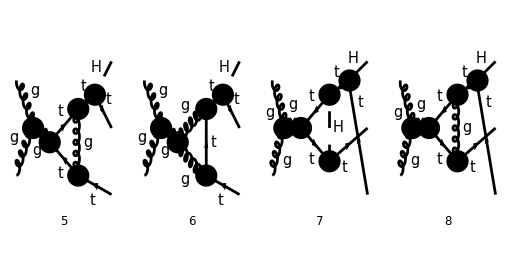

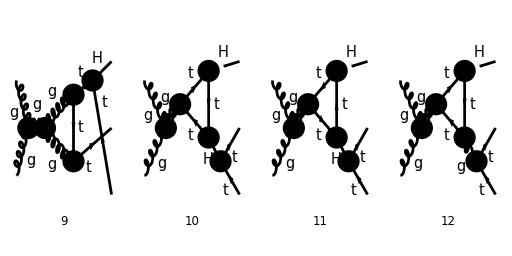

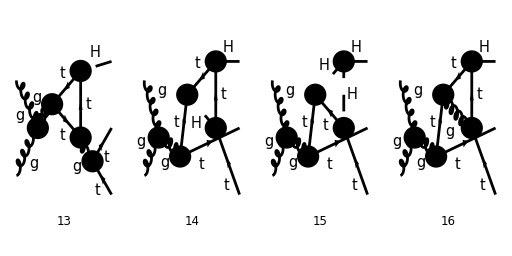

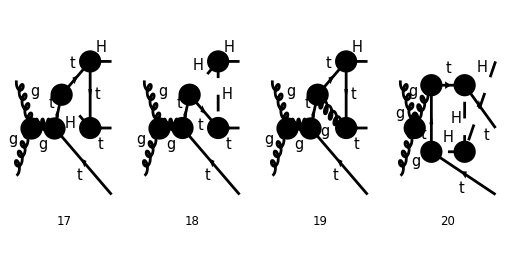

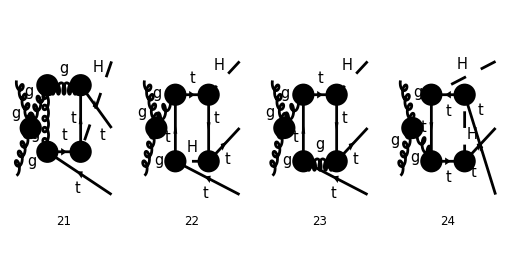

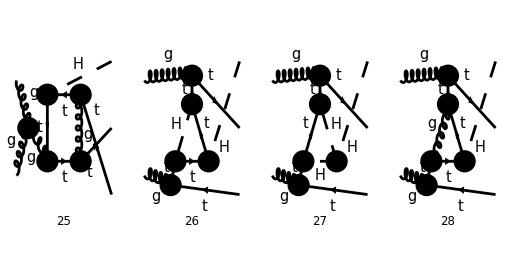

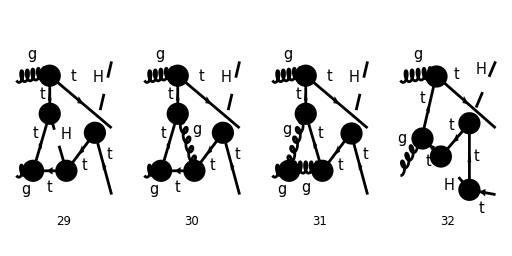

```mathematica
diagsggHqq=InsertFields[CreateTopologies[1,2->3,ExcludeTopologies->{Tadpoles,WFCorrections}],{V[5],V[5]}-> {S[1], F[3,{3}], -F[3,{3}]}, InsertionLevel->{Particles},Model->"SMQCD", ExcludeParticles->{F[4],F[3,{1}],F[3,{2}], V[1],V[2],V[3],V[4], S[2], S[3]}];

Paint[DiagramSelect[diagsggHqq, FreeQ[LoopFields[##], V[5]]&],ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```